SupportVectorMachine-Accuracy:0.786

SupportVectorMachine-Precision:<|negative→0.75619,positive→0.818947|>

SupportVectorMachine-Recall:<|negative→0.821946,positive→0.752418|>

SupportVectorMachine-ROC:Missing[KeyAbsent,1]Missing[KeyAbsent,2]

DecisionTree-Accuracy:0.74

DecisionTree-Precision:<|negative→0.709193,positive→0.775161|>

DecisionTree-Recall:<|negative→0.782609,positive→0.700193|>

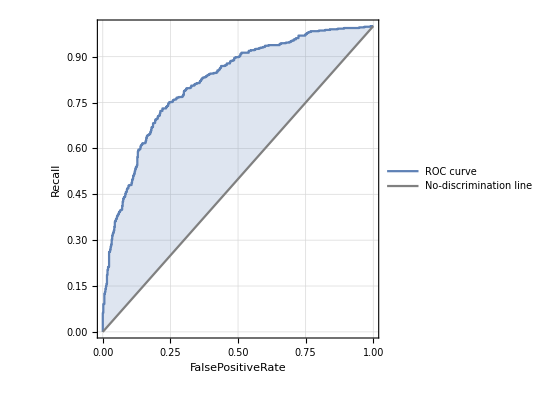
DecisionTree-ROC:-Graphics--Graphics-

NeuralNetwork-Accuracy:0.77

NeuralNetwork-Precision:<|negative→0.788155,positive→0.755793|>

NeuralNetwork-Recall:<|negative→0.716356,positive→0.820116|>

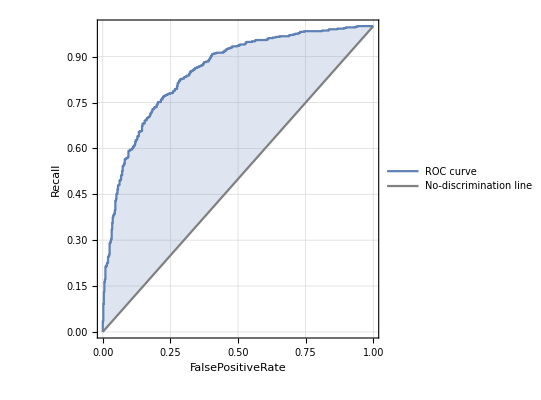
NeuralNetwork-ROC:-Graphics--Graphics-

```mathematica
(*This program might take around 2 to 5 minutes to finish*)
(*README: Due to the limit of time and computation space we set the amount of data to 5000, however the results we shown in the slides are based on 50,000 data, since it took a relatively longer time, we set the amount of data to 5000 here, just to show that the program is working*)
SetDirectory[NotebookDirectory[]];
raw = OpenRead["reviews.csv"];
reviews = Map[StringSplit[#, "|"]&, ReadList[raw, String]];
(*start pre-processing data*)
(*spell checking, tokenization, remove symbols*)
(*extract words from dataset*)
numOfReviews=Length[reviews];
indexOfReviews=2;
$RecursionLimit=Infinity;
reviewsWords = List[];
While[indexOfReviews≤ 5000,
review=reviews[[indexOfReviews]];
(*extract review string from all reviews*)
reviewStr=review[[2]];
(*Delete stop words*)
newReviewStr = DeleteStopwords[reviewStr];
(*Extract words from string*)
reviewWords=TextWords[newReviewStr];
(*change the word to its stem*)
reviewWords = WordStem[reviewWords];
(*change the word to lower case*)
reviewWords = ToLowerCase[reviewWords];
(*delete duplicate word in the review*)
reviewWords = DeleteDuplicates[reviewWords];
numOfWords = Length[reviewWords];
indexOfWord = 1;
indexesOfDeleteWord = List[];
correctedReviewWords = List[];
(*check the spell of the word and get rid of symbols*)
While[indexOfWord ≤ numOfWords,
If[DictionaryWordQ[reviewWords[[indexOfWord]]] == True,correctedReviewWords = Append[correctedReviewWords, reviewWords[[indexOfWord]]];
];
indexOfWord++;
];
reviewsWords = Append[reviewsWords, correctedReviewWords];
indexOfReviews++;
];

(*feature extractor TF-IDF*)
fe=FeatureExtraction[reviewsWords,"TFIDF"];
features=fe[reviewsWords];
listOfFeatures=List@@features;
(*reduce the dimension of features of reivews*)
listOfFeatures = DimensionReduce[listOfFeatures, 100];
(*generate test data and training data*)
testData=Take[listOfFeatures,{1,-1,5}];
trainData=Drop[listOfFeatures,{1,-1,5}];
indexOfReviews=2;
classes=List[];
(*generate the target value*)
While[indexOfReviews≤5000,
review=reviews[[indexOfReviews]];
class=Take[review,1];
classes=Append[classes,class[[1]]];
indexOfReviews++;
];
testClasses=Take[classes,{1,-1,5}];
trainClasses=Drop[classes,{1,-1,5}];
(*generate training set and testing set*)
trainingSet=trainData->trainClasses;
testingSet = testData -> testClasses;
(*train the classifiers*)
svm=Classify[trainingSet,Method->"SupportVectorMachine"];
rf = Classify[trainingSet, Method->"RandomForest"];
nn = Classify[trainingSet, Method->"NeuralNetwork"];
(*evaluate the classifier*)
svmCM = ClassifierMeasurements[svm, testingSet];
rfCM = ClassifierMeasurements[rf, testingSet];
nnCM = ClassifierMeasurements[nn, testingSet];
Print["SupportVectorMachine-Accuracy:",svmCM["Accuracy"]]
Print["SupportVectorMachine-Precision:",svmCM["Precision"]]
Print["SupportVectorMachine-Recall:",svmCM["Recall"]]
Print["SupportVectorMachine-ROC:",svmCM["ROCCurve"][1], svmCM["ROCCurve"][2]]
Print["DecisionTree-Accuracy:",rfCM["Accuracy"]]
Print["DecisionTree-Precision:",rfCM["Precision"]]
Print["DecisionTree-Recall:",rfCM["Recall"]]
Print["DecisionTree-ROC:",rfCM["ROCCurve"][[1]], rfCM["ROCCurve"][[1]]]
Print["NeuralNetwork-Accuracy:",nnCM["Accuracy"]]
Print["NeuralNetwork-Precision:",nnCM["Precision"]]
Print["NeuralNetwork-Recall:",nnCM["Recall"]]
Print["NeuralNetwork-ROC:",nnCM["ROCCurve"][[1]], nnCM["ROCCurve"][[1]]]
```